## dσ/dY

```mathematica
(*                                         -Graphics-                                 *)
```

Photon spectrum for Electron

```mathematica
Clear["Global`*"]
```

```mathematica
α=1/137;
me=0.000511;  (* Mass of electron in GeV *)
Ee = 50;             (* Energy of electron beam in GeV *)
FEe = 1;
FMe =1;

q2mine[ye_]:=(me^2  ye^2)/(1-ye);  
q2maxe= 100000;
```

```mathematica
PhotonFluxElectron[ye_?NumericQ,prec_:MachinePrecision]:=1/ye* α/π*NIntegrate[((1-ye)(1-q2mine[ye]/q2)FEe +  ye^2/2 FMe) 1/q2 ,{q2,q2mine[ye],q2maxe}, MaxRecursion -> 100];  (* //Simplify *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

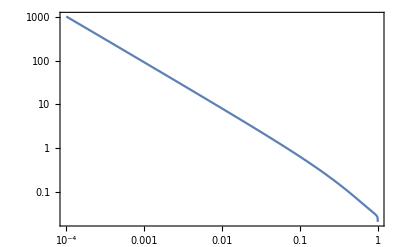

```mathematica
LogLogPlot[PhotonFluxElectron[ye],{ye,0.0001,0.9999},PlotRange->Full,Frame->True]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

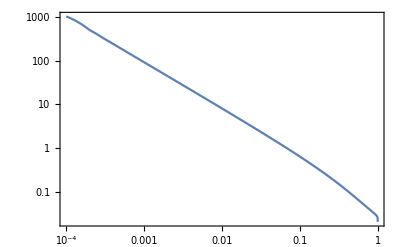

```mathematica
PhotonFluxElectronList=ParallelTable[Flatten[{ye, PhotonFluxElectron[ye]}],{ye,0.0001,0.9999,0.0001}];
funPhotonFluxElectronList=Interpolation[PhotonFluxElectronList]
PhotonFluxElectronFinal=FunctionInterpolation[funPhotonFluxElectronList[ye],{ye,0.0001,0.9999}]
LogLogPlot[PhotonFluxElectronFinal[ye],{ye,0.0001,0.9999},Frame->True]
```

Photon spectrum for Proton (Elastic)

```mathematica
α=1/137;
mp=0.938;  (* Mass of proton in GeV *)
Ep= 7000;   (* Energy of proton beam in GeV *)

GE2[q2_]:=(1+q2/0.71)^{-4}; 
GM2[q2_]:=7.78*GE2[q2]; 

FE[q2_]:=(4  mp^2  GE2[q2]+ q2  GM2[q2])/(4 mp^2 + q2);  (* Electric Form Factor *)
FM[q2_]:=GM2[q2];                                                                                     (* Magnetic Form Factor *)

Plot[FE[q2],{q2,1,1000},Frame->True];
Plot[FM[q2],{q2,1,1000},Frame->True];

q2minp[yp_]:=(mp^2  yp^2)/(1-yp);   (* For the case of elastic *)
q2maxp = 100000;
```

```mathematica
PhotonFluxProton[yp_,prec_:MachinePrecision]:=1/yp*α/π*NIntegrate[((1-yp)(1-q2minp[yp]/q2)*FE[q2] +  yp^2/2 *FM[q2]) 1/q2 ,{q2,q2minp[yp],q2maxp}, MaxRecursion -> 100(*,PrecisionGoal->12,AccuracyGoal->15,WorkingPrecision->10*)]; (* //Simplify *)
```

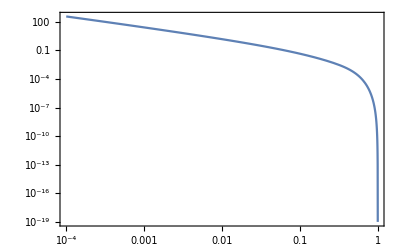

```mathematica
LogLogPlot[PhotonFluxProton[yp],{yp,0.0001,0.9999},PlotRange->Full,Frame->True]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

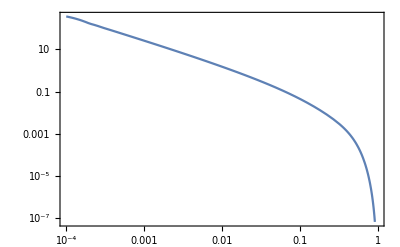

```mathematica
PhotonFluxProtonList=ParallelTable[Flatten[{yp, PhotonFluxProton[yp]}],{yp,0.0001,0.9999,0.0001}];
funPhotonFluxProtonList=Interpolation[PhotonFluxProtonList]
PhotonFluxProtonFinal=FunctionInterpolation[funPhotonFluxProtonList[yp],{yp,0.0001,0.9999}]
LogLogPlot[PhotonFluxProtonFinal[yp],{yp,0.0001,0.9999},Frame->True]
```

```mathematica
csSleptonsWDraft[wvalue_]:=Module[{msleptons,hbarc2,alpha2,beta,cs},

msleptons=100.0;

hbarc2=0.389;
alpha2=(1.0/137.0)*(1.0/137.0);

(*Element-wise calculation of beta using If*)beta=Sqrt[If[1.0-4.0*msleptons*msleptons/wvalue^2.0>=0,1.0-4.0*msleptons*msleptons/wvalue^2.0,Indeterminate]];
(*Element-wise calculation of cs using If*)cs=If[wvalue>msleptons,(2.0*Pi*alpha2*hbarc2)/wvalue^2.0*(beta)*(2.0-beta^2.0-(1.0-beta^4.0)/(2.0*beta)*Log[(1.0+beta)/(1.0-beta)]),0.0]*1*^9;
cs]

(*Example usage*)
wvalue=200.1;
result=csSleptonsWDraft[wvalue]
```

0.102672

```mathematica
Ee = 50;
Ep=7000;
Sqrts= √(4 Ee Ep);                                  (* 1200 Center of mass energy in GeV *)

yp[W_,Y_]:=W ⅇ^Y/(2 Ep);
ye[W_,Y_]:=W ⅇ^-Y/(2 Ee);
```

```mathematica
Flux[W_,Y_]:=Re[PhotonFluxElectronFinal[ye[W,Y]]*PhotonFluxProtonFinal[yp[W,Y]]*Boole[0<=yp[W,Y]<=1]*Boole[0<=ye[W,Y]<=1]];
```

```mathematica
dSigmadY=ParallelTable[Flatten[{Y,2.0/Sqrts^2.0*NIntegrate[csSleptonsWDraft[W]* W * Flux[W,Y],{W,200.1,Sqrts},MaxRecursion->100]}],{Y,0.0,5.0,0.01}];
```

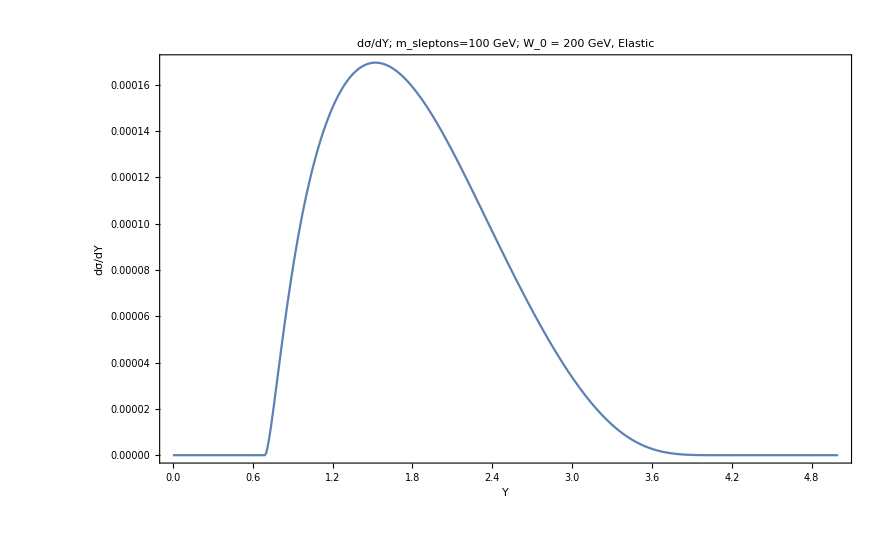

```mathematica
ListPlot[dSigmadY,PlotRange->All,PlotLabel->TraditionalForm["dσ/dY; m_sleptons=100 GeV; W_0 = 200 GeV, Elastic"],FrameLabel->{"Y","dσ/dY"},Frame->True,Joined->True]
```

```mathematica
Export["slepton.pdf",%]
```

slepton.pdf